Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→ProductLog[-Log[e]]/Log[e]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→1.00274-90.7671 ⅈ},{m→0.0541801+0. ⅈ},{m→1.2806+3.72211 ⅈ}}

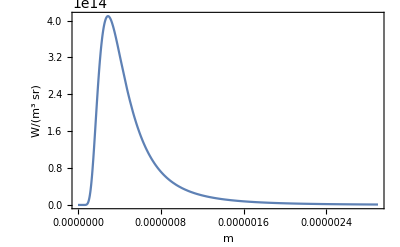

```mathematica
(* Part 1 *)
Solve[e^r+1/r==0, r]
Solve[Zeta[m]+1/(Zeta[m])^2==E,m]//N
PlanckRadiationLaw[Quantity[10000, "Kelvins"], "SpectralPlot"]
```

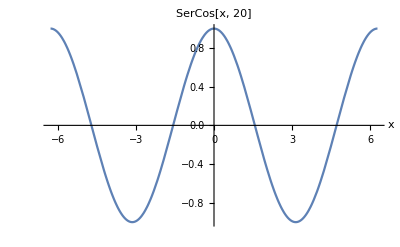

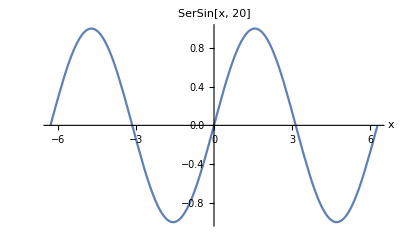

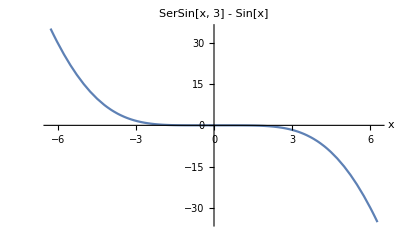

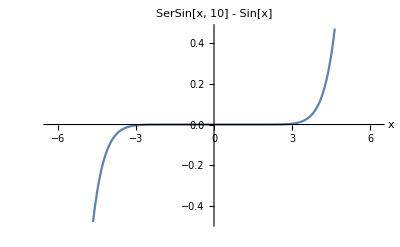

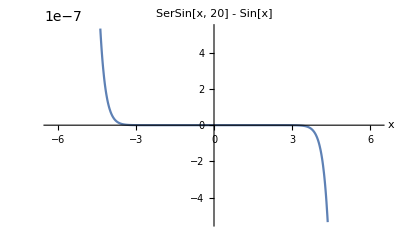

-Graphics-

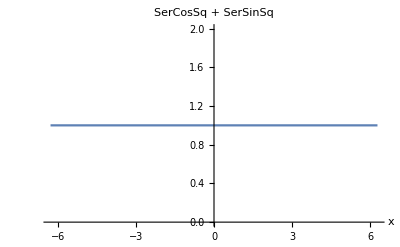

```mathematica
(* Part 2 *)
(* Define series expansions of cos and sin *)
SerCos[x_, n_] := Normal[Series[Cos[u], {u, 0, n}]]/.u->x
SerSin[x_, n_] := Normal[Series[Sin[u], {u, 0, n}]]/.u->x

(* Plot series expansions *)
Plot[SerCos[x, 20], {x, -2*Pi, 2*Pi},
	PlotLabel->"SerCos[x, 20]",
	AxesLabel->Automatic]

Plot[SerSin[x, 20], {x, -2*Pi, 2*Pi},
	PlotLabel->"SerSin[x, 20]",
	AxesLabel->Automatic]

(* Plot difference between SerSin and Sin *)
Plot[SerSin[x, 3] - Sin[x],{x, -2*Pi, 2*Pi}, 
	PlotLabel->"SerSin[x, 3] - Sin[x]",
	AxesLabel->Automatic]
Plot[SerSin[x, 10] - Sin[x],{x, -2*Pi, 2*Pi}, 
	PlotLabel->"SerSin[x, 10] - Sin[x]",
	AxesLabel->Automatic]
Plot[SerSin[x, 20] - Sin[x],{x, -2*Pi, 2*Pi}, 
	PlotLabel->"SerSin[x, 20] - Sin[x]",
	AxesLabel->Automatic]

(* Define series expansions of cos^2 and sin^2 *)
SerCosSq[x_, n_]:=Normal[Series[Cos[u]^2, {u, 0, n}]]/.u->x
SerSinSq[x_, n_]:= Normal[Series[Sin[u]^2, {u, 0, n}]]/.u->x

(* Plot SerCos^2 + SerSin^2 *)
(*
	The graph diverges as x -> 2*Pi (or any boundary value). This is because the errors in the series expansions of Sin and Cos are compounded when they are squared and added together. 
*)
Plot [SerCos[x, 5]^2+SerSin[x, 5]^2, {x, -100*Pi, 100*Pi},
	PlotLabel->"SerCos^2 + SerSin^2"]

(* Plot SerCosSq + SerSinSq *)
(*
	The graph gives the expected behaviour because the error in adding the series expansion of Sin^2 and Cos^2 is smaller than the error in calculating Sin^2 + Cos^2 from the series expansion of Sin and Cos.
*)
Plot[SerCosSq[x, 5]+SerSinSq[x, 5], {x, -2*Pi, 2*Pi},
	PlotLabel->"SerCosSq + SerSinSq",
	AxesLabel->Automatic]
```

```mathematica
(* Part 3 *)
(* Rotation matrices *)
x [ϕ_]= {{1, 0, 0},{0, Cos[ϕ], -Sin[ϕ]},{0, Sin[ϕ], Cos[ϕ]}};
z[ψ_]= {{Cos[ψ], -Sin[ψ], 0},{Sin[ψ], Cos[ψ], 0}, {0, 0, 1}};

(* General rotation matrix *)
Rot3 = z[ψ].x[ϕ].z[ψ];
Simplify[Rot3]
(* Inverse matrix *)
Rot3Inverse1 =  z[-ψ].x[-ϕ].z[-ψ];
Simplify[Rot3Inverse1]
Rot3Inverse2 = Simplify[Inverse[Rot3]]
prod1=Simplify[Rot3Inverse1.Rot3]
prod2=Simplify[Rot3Inverse2.Rot3]
prod1-prod2
```

{{Cos[ψ]^2-Cos[ϕ] Sin[ψ]^2,-(1+Cos[ϕ]) Cos[ψ] Sin[ψ],Sin[ϕ] Sin[ψ]},{(1+Cos[ϕ]) Cos[ψ] Sin[ψ],Cos[ϕ] Cos[ψ]^2-Sin[ψ]^2,-Cos[ψ] Sin[ϕ]},{Sin[ϕ] Sin[ψ],Cos[ψ] Sin[ϕ],Cos[ϕ]}}

{{Cos[ψ]^2-Cos[ϕ] Sin[ψ]^2,(1+Cos[ϕ]) Cos[ψ] Sin[ψ],Sin[ϕ] Sin[ψ]},{-(1+Cos[ϕ]) Cos[ψ] Sin[ψ],Cos[ϕ] Cos[ψ]^2-Sin[ψ]^2,Cos[ψ] Sin[ϕ]},{Sin[ϕ] Sin[ψ],-Cos[ψ] Sin[ϕ],Cos[ϕ]}}

{{Cos[ϕ]^2 Cos[ψ]^2+Cos[ψ]^2 Sin[ϕ]^2-Cos[ϕ] Sin[ψ]^2,(1+Cos[ϕ]) Cos[ψ] Sin[ψ],Sin[ϕ] Sin[ψ]},{-(1+Cos[ϕ]) Cos[ψ] Sin[ψ],1/4 (-2+2 Cos[ϕ]+Cos[ϕ-2 ψ]+2 Cos[2 ψ]+Cos[ϕ+2 ψ]),Cos[ψ] Sin[ϕ]},{Sin[ϕ] Sin[ψ],-Cos[ψ] Sin[ϕ],Cos[ϕ]}}

{{1,0,0},{0,1,0},{0,0,1}}

{{1,0,0},{0,1,0},{0,0,1}}

{{0,0,0},{0,0,0},{0,0,0}}